```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"xv_Q2_CT14_positive_valence_ud_sea_ud.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

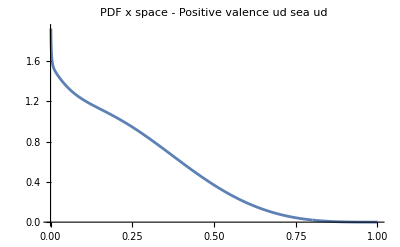

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"PDF x space - Positive valence ud sea ud",PlotRange->All]
```

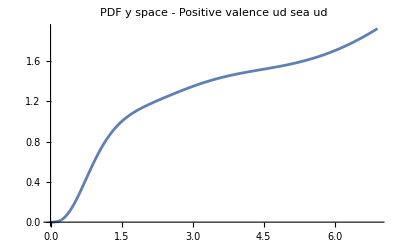

```mathematica
ListLinePlot[Transpose[{-Log[col1],col2}],PlotLabel->"PDF y space - Positive valence ud sea ud",PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"interp.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

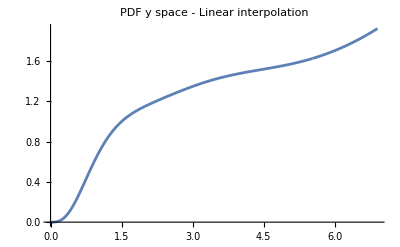

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"PDF y space - Linear interpolation",PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"y_xv_Q2_CT14_positive_valence_ud_sea_ud.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

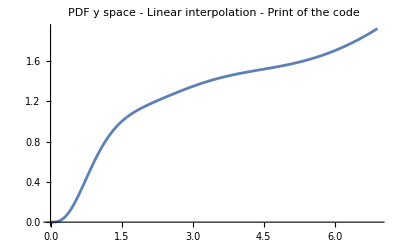

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"PDF y space - Linear interpolation - Print of the code",PlotRange->All]
```

```mathematica
Clear[col1]
Clear[col2]
Clear[data]
```

```mathematica
data = Import[NotebookDirectory[]<>"Y_fourier_transform_absolute.dat","Table"];
```

```mathematica
col1=data[[All,1]];
col2=data[[All,2]];
```

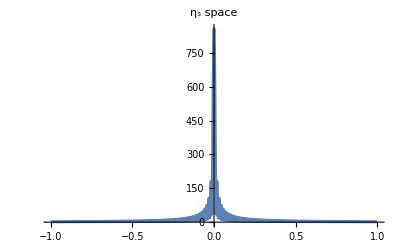

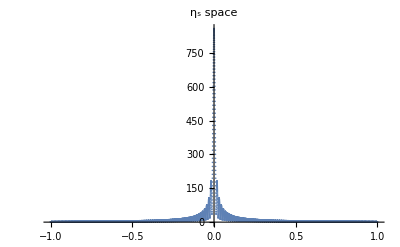

```mathematica
ListLinePlot[Transpose[{col1,col2}],PlotLabel->"η_s space",PlotRange->All]
ListPlot[Transpose[{col1,col2}],PlotLabel->"η_s space",PlotRange->All]
```